```mathematica
(* ECUACIONES *)

(******************************************************************************)
(* FRECUENCIAS FASE NORMAL*)
(******************************************************************************)

Clear[ωzxn,ωzyn];
Clear[ω,ωo]
ω=1;
ωo=1;
(* ωzxn Frecuencia dependendiente z-x Fase Normal *)
ωzxn[ηz_,ηx_]:=ωo*√(1-(ηz-ηx)/ωo); 
(* ωzyn Frecuencia dependendiente z-y Fase Normal *)
ωzyn[ηz_,ηy_]:=1-(ηz-ηy)/ωo; 

(******************************************************************************)
(* FRECUENCIAS FASE SUPERRADIANTE *)
(******************************************************************************)

Clear[μx,ω1,ω2,ω3,ω4,ω5,ωzxs1,ωzxs2,ωzys1,ωzys2];
(* Resultado de eliminar términos lineales *)
μx[ηz_,ηx_,γ_,ξ_]:=1/((γ^2*(1+ξ)^2)/(ω*ωo)+(ηz-ηx)/ωo);

(* ω1 Frecuencia relacionada con d^*d *)
ω1[ηz_,ηx_,γ_,ξ_]:=1/2((ωo/μx[ηz,ηx,γ,ξ]-ηz)*(1+μx[ηz,ηx,γ,ξ])+ηx*(1-μx[ηz,ηx,γ,ξ]));


(* ω2 Frecuencia relacionada con (d^*+d)^2 *)
ω2[ηz_,ηx_,γ_,ξ_]:=1/8*(1-μx[ηz,ηx,γ,ξ])*(ωo/(1+μx[ηz,ηx,γ,ξ])*(3+μx[ηz,ηx,γ,ξ])/μx[ηz,ηx,γ,ξ]+ηz+ηx*(3*μx[ηz,ηx,γ,ξ]^2-2*μx[ηz,ηx,γ,ξ]+3)/(1-μx[ηz,ηx,γ,ξ]^2));

(* ω3 Frecuencia relacionada con (c^*+c)(d^*+d) *)
ω3[ηz_,ηx_,γ_,ξ_]:=-(√2)/4*γ*(1+ξ)*(1-μx[ηz,ηx,γ,ξ])/Sqrt[1+μx[ηz,ηx,γ,ξ]];


(* ω4 Frecuencia relacionada con (cd^* + c^*d)(...) *)
ω4[ηz_,ηx_,γ_,ξ_]:=γ*Sqrt[1/2*(1+μx[ηz,ηx,γ,ξ])];

(* ω5 Frecuencia relacionada con (d^*-d)^2 *)
ω5[ηz_,ηx_,ηy_,γ_,ξ_]:=-1/8*ηy*(1+μx[ηz,ηx,γ,ξ]);

(* Frecuencias compuestas zx *)
ωzxs1[ηz_,ηx_,γ_,ξ_]:=ω1[ηz,ηx,γ,ξ]^2+4*ω2[ηz,ηx,γ,ξ]*ω1[ηz,ηx,γ,ξ] ;

ωzxs2[ηz_,ηx_,γ_,ξ_]:=Sqrt[ω*ω1[ηz,ηx,γ,ξ]]*(4*ω3[ηz,ηx,γ,ξ]+2*ω4[ηz,ηx,γ,ξ]*(1+ξ));

(* Frecuencias compuestas zy *)
ωzys1[ηz_,ηx_,ηy_,γ_,ξ_]:=1-(4*ω5[ηz,ηx,ηy,γ,ξ])/ω1[ηz,ηx,γ,ξ];
ωzys2[ηz_,ηx_,ηy_,γ_,ξ_]:=(2*ω4[ηz,ηx,γ,ξ]*(1-ξ))/Sqrt[ω*ω1[ηz,ηx,γ,ξ]]

(******************************************************************************)
(* Energías de oscilador *)
(******************************************************************************)

(**************************)
(* Energía del oscilador 1 *)
(***************************)

Clear[ϵ1pn,ϵ1ps,ϵ1mn,ϵ1ms];
(* Energía 1+ Fase Normal *)
ϵ1pn[ηz_,ηx_,γ_,ξ_]:=Sqrt[1/2*(ω^2+ωzxn[ηz,ηx]^2+√((ωzxn[ηz,ηx]^2-ω^2)^2+4*γ^2*ω*ωzxn[ηz,ηx]*(1+ξ)^2))];
(* Energía 1- Fase Normal *)
ϵ1mn[ηz_,ηx_,γ_,ξ_]:=Sqrt[1/2*(ω^2+ωzxn[ηz,ηx]^2-√((ωzxn[ηz,ηx]^2-ω^2)^2+4*γ^2*ω*ωzxn[ηz,ηx]*(1+ξ)^2))];
(* Energía 1+ Fase Superradiante *)
ϵ1ps[ηz_,ηx_,γ_,ξ_]:=Sqrt[1/2*(ω^2 + ωzxs1[ηz,ηx,γ,ξ] + Sqrt[(ωzxs1[ηz,ηx,γ,ξ] - ω^2)^2 + ωzxs2[ηz,ηx,γ,ξ]^2] )];
(* Energía 1- Fase Superradiante *)
ϵ1ms[ηz_,ηx_,γ_,ξ_]:=Sqrt[1/2*(ω^2 + ωzxs1[ηz,ηx,γ,ξ] - Sqrt[(ωzxs1[ηz,ηx,γ,ξ] - ω^2)^2 + ωzxs2[ηz,ηx,γ,ξ]^2] )];
(**************************)
(* Energía del oscilador 2 *)
(***************************)
Clear[ϵ2pn,ϵ2ps,ϵ2mn,ϵ2ms];

(* Energía 2+ Fase Normal *)
ϵ2pn[ηz_,ηy_,γ_,ξ_]:=Sqrt[1/2*(1+ωzyn[ηz,ηy]+√((ωzyn[ηz,ηy]^2-1)^2+(4*γ^2*(1-ξ)^2)/(ω*ωo)))];
(* Energía 2- Fase Normal *)
ϵ2mn[ηz_,ηy_,γ_,ξ_]:=Sqrt[1/2*(1+ωzyn[ηz,ηy]-√((ωzyn[ηz,ηy]^2-1)^2+(4*γ^2*(1-ξ)^2)/(ω*ωo)))];
(* Energía 2+ Fase Superradiante *)
ϵ2ps[ηz_,ηx_,ηy_,γ_,ξ_]:=Sqrt[1/2*(1+ωzys1[ηz,ηx,ηy,γ,ξ]+Sqrt[(ωzys1[ηz,ηx,ηy,γ,ξ]-1)^2 + ωzys2[ηz,ηx,ηy,γ,ξ]^2])];
(* Energía 2- Fase Superradiante *)
ϵ2ms[ηz_,ηx_,ηy_,γ_,ξ_]:=Sqrt[1/2*(1+ωzys1[ηz,ηx,ηy,γ,ξ]-Sqrt[(ωzys1[ηz,ηx,ηy,γ,ξ]-1)^2 +ωzys2[ηz,ηx,ηy,γ,ξ]^2])];
Manipulate[Plot[{Re[(ϵ1mn[ηz,ηx,γ,ξ]*ϵ2mn[ηz,ηy,γ,ξ])],Re[(ϵ1ms[ηz,ηx,γ,ξ]*ϵ2ms[ηz,ηx,ηy,γ,ξ])],Re[(ϵ1pn[ηz,ηx,γ,ξ]*ϵ2pn[ηz,ηy,γ,ξ])],Re[(ϵ1ps[ηz,ηx,γ,ξ]*ϵ2ps[ηz,ηx,ηy,γ,ξ])]},{γ,-2,2},PlotRange->{{-2,2},{-3,3}},
GridLines->{{{Sqrt[ω*ωo]/(1+ξ)*Sqrt[1-(ηz-ηx)/ωo],Dashed},{Sqrt[ω*ωo]/(1-ξ)*Sqrt[1-(ηz-ηy)/ωo],Dotted}},None},GridLinesStyle->Black,Exclusions->All],{ηz,0,1},{ηy,0,1},{ηx,0,1},{ξ,0,1}]
```

Power::infy: Infinite expression 1/0 encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

Power::infy: Infinite expression 1/0 encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

Power::infy: Infinite expression 1/0 encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

Power::infy: Infinite expression 1/0 encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

Power::infy: Infinite expression 1/0 encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

Power::infy: Infinite expression 1/0 encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

Power::infy: Infinite expression 1/0 encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

Infinity::indet: Indeterminate expression 0 ComplexInfinity encountered.

General::stop: Further output of Infinity::indet will be suppressed during this calculation.

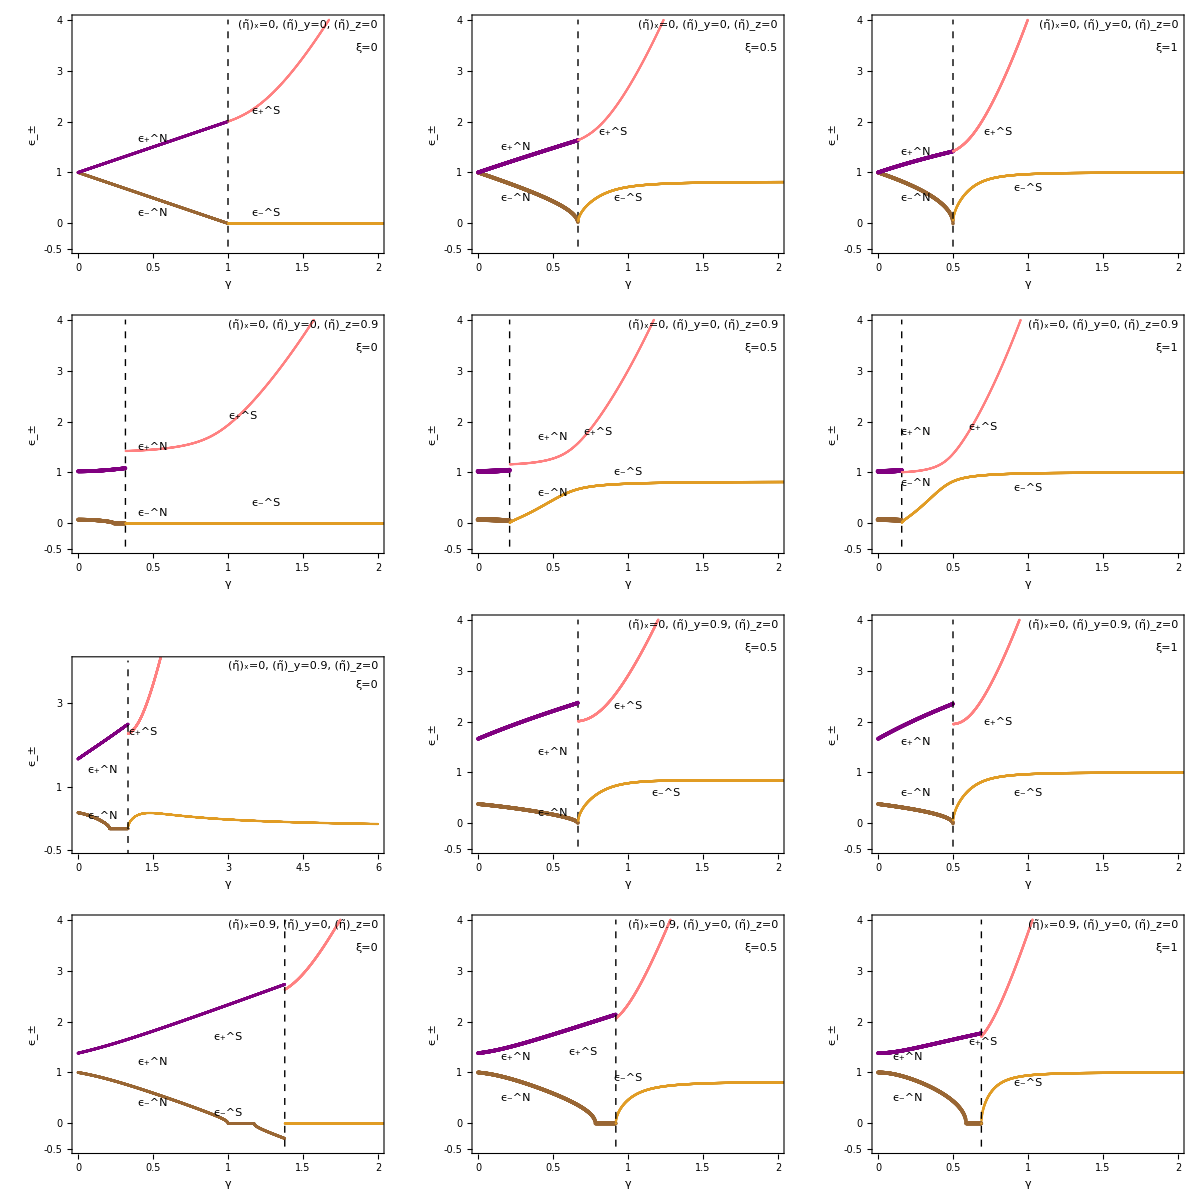

```mathematica
SetDirectory["/Users/rich/Documentos/06 Trimestre/Tesis/Campo medio/Soteira/Imagenes"];
Clear[d];
d=0.001;
Clear[xc]
xc[ηx_,ηy_,ηz_,ξ_]:=Sqrt[ω*ωo]/(1+ξ)*Sqrt[1-(ηz-ηx)/ωo];

Clear[t1,t2,t3,t4]
t1[ηx_,ηy_,ηz_,ξ_]:=Table[{γ,Re[(ϵ1mn[ηz,ηx,γ,ξ]*ϵ2mn[ηz,ηy,γ,ξ])]},{γ,0,xc[ηx,ηy,ηz,ξ],d}];


t2[ηx_,ηy_,ηz_,ξ_]:=Table[{γ,Re[(ϵ1ms[ηz,ηx,γ,ξ]*ϵ2ms[ηz,ηx,ηy,γ,ξ])]},{γ,xc[ηx,ηy,ηz,ξ],4,d}];
(* Tabla Extra*)
t2a[ηx_,ηy_,ηz_,ξ_]:=Table[{γ,Re[(ϵ1ms[ηz,ηx,γ,ξ]*ϵ2ms[ηz,ηx,ηy,γ,ξ])]},{γ,xc[ηx,ηy,ηz,ξ],6,d}];
(***************)

t3[ηx_,ηy_,ηz_,ξ_]:=Table[{γ,Re[(ϵ1pn[ηz,ηx,γ,ξ]*ϵ2pn[ηz,ηy,γ,ξ])]},{γ,0,xc[ηx,ηy,ηz,ξ],d}];
t4[ηx_,ηy_,ηz_,ξ_]:=Table[{γ,Re[(ϵ1ps[ηz,ηx,γ,ξ]*ϵ2ps[ηz,ηx,ηy,γ,ξ])]},{γ,xc[ηx,ηy,ηz,ξ],4,d}];
(*Tabla Extra*)
t4a[ηx_,ηy_,ηz_,ξ_]:=Table[{γ,Re[(ϵ1ps[ηz,ηx,γ,ξ]*ϵ2ps[ηz,ηx,ηy,γ,ξ])]},{γ,xc[ηx,ηy,ηz,ξ],4,d}];
(***************)




(*Variables del plot*)
Clear[cB,cT]
cB=Black;
cT=Transparent;
align[Center]={0,0};  
Clear[pt1,pt2,pt3,pt4]
pt1[ηx_,ηy_,ηz_,ξ_,ejex_,ejey_,x1_,y1_,x2_,y2_,x3_,y3_,x4_,y4_]:=ListPlot[t1[ηx,ηy,ηz,ξ],
Joined->True,
Mesh->All,
Frame->True,
PlotRange->{{0,2},{-0.5,4}},
FrameTicks->{{{-0.5,0,1,2,3,4},None},{{0,0.5,1,1.5,2},None}},
FrameLabel->{Style["γ",FontSize->15,ejex],Style["ϵ_±",FontSize->15,ejey]},
PlotStyle->Brown,
ImageSize->{360,234},
Epilog->{Text["ϵ_-^N",{x1,y1},align[Center]],
Text["ϵ_-^S",{x2,y2},align[Center]],
Text["ϵ_+^N",{x3,y3},align[Center]],
Text["ϵ_+^S",{x4,y4},align[Center]],
Inset[Framed[Style["\!\(\*SubscriptBox[OverscriptBox[\(η\), \(~\)], \(x\)]\)="<>ToString[ηx]<>", \!\(\*SubscriptBox[OverscriptBox[\(η\), \(~\)], \(y\)]\)="<>ToString[ηy]<>", \!\(\*SubscriptBox[OverscriptBox[\(η\), \(~\)], \(z\)]\)="<>ToString[ηz],10],Background->LightYellow],{2,4.01},{1,1}],Inset[Framed[Style["ξ="<>ToString[ξ],10],Background->LightYellow],{2,3.55},{1,1}],{Dashed,Line[{{xc[ηx,ηy,ηz,ξ],-1},{xc[ηx,ηy,ηz,ξ],4}}]}(*,{Red,Line[{{Sqrt[ω*ωo]/(1-ξ)*Sqrt[1-(ηz-ηy)/ωo],-1},{Sqrt[ω*ωo]/(1-ξ)*Sqrt[1-(ηz-ηy)/ωo],3}}]}*)}]

(*Gráfica Extra*)
pt1a[ηx_,ηy_,ηz_,ξ_,ejex_,ejey_,x1_,y1_,x2_,y2_,x3_,y3_,x4_,y4_]:=ListPlot[t1[ηx,ηy,ηz,ξ],
Joined->True,
Mesh->All,
Frame->True,
PlotRange->{{0,6},{-0.5,4}},
FrameTicks->{{{-0.5,0,1,2,3,4,5,6},None},{{0,0.5,1,1.5,2,2.5,3,3.5,4,4.5,5,5.5,6},None}},
FrameLabel->{Style["γ",FontSize->15,ejex],Style["ϵ_±",FontSize->15,ejey]},
PlotStyle->Brown,
ImageSize->{360,234},
Epilog->{Text["ϵ_-^N",{x1,y1},align[Center]],
Text["ϵ_-^S",{x2,y2},align[Center]],
Text["ϵ_+^N",{x3,y3},align[Center]],
Text["ϵ_+^S",{x4,y4},align[Center]],
Inset[Framed[Style["\!\(\*SubscriptBox[OverscriptBox[\(η\), \(~\)], \(x\)]\)="<>ToString[ηx]<>", \!\(\*SubscriptBox[OverscriptBox[\(η\), \(~\)], \(y\)]\)="<>ToString[ηy]<>", \!\(\*SubscriptBox[OverscriptBox[\(η\), \(~\)], \(z\)]\)="<>ToString[ηz],10],Background->LightYellow],{6,4.01},{1,1}],Inset[Framed[Style["ξ="<>ToString[ξ],10],Background->LightYellow],{6,3.55},{1,1}],{Dashed,Line[{{xc[ηx,ηy,ηz,ξ],-1},{xc[ηx,ηy,ηz,ξ],4}}]}(*,{Red,Line[{{Sqrt[ω*ωo]/(1-ξ)*Sqrt[1-(ηz-ηy)/ωo],-1},{Sqrt[ω*ωo]/(1-ξ)*Sqrt[1-(ηz-ηy)/ωo],3}}]}*)}]

(***************)

pt2[ηx_,ηy_,ηz_,ξ_]:=ListPlot[t2[ηx,ηy,ηz,ξ],
Joined->True,
Mesh->All,Frame->True,
FrameTicks->{{{0,1,2,3,4},None},{{0,0.5,1,1.5,2},None}},
PlotRange->{{0,2},{0,4}},
PlotStyle->ColorData[97,2],
ImageSize->{360,234}
];
(* Gráfica Extra*)
Clear[pt2a]
pt2a[ηx_,ηy_,ηz_,ξ_]:=ListPlot[t2a[ηx,ηy,ηz,ξ],
Joined->True,
Mesh->All,Frame->True,
FrameTicks->{{{0,1,2,3,4,5,6},None},{{0,0.5,1,1.5,2},None}},
PlotRange->{{0,2},{0,6}},
PlotStyle->ColorData[97,2],
ImageSize->{360,234}
];
(***************)


pt3[ηx_,ηy_,ηz_,ξ_]:=ListPlot[t3[ηx,ηy,ηz,ξ],
Joined->True,
Mesh->All,Frame->True,
FrameTicks->{{{0,1,2,3,4},None},{{0,0.5,1,1.5,2},None}},
PlotRange->{{0,2},{0,4}},
PlotStyle->Purple,
ImageSize->{360,234}
];
pt4[ηx_,ηy_,ηz_,ξ_]:=ListPlot[t4[ηx,ηy,ηz,ξ],
Joined->True,
Mesh->All,Frame->True,
FrameTicks->{{{0,1,2,3,4},None},{{0,0.5,1,1.5,2},None}},
PlotRange->{{0,2},{0,4}},
PlotStyle->Pink,
ImageSize->{360,234}
];

(* Gráfica Extra*)
pt4a[ηx_,ηy_,ηz_,ξ_]:=ListPlot[t4a[ηx,ηy,ηz,ξ],
Joined->True,
Mesh->All,Frame->True,
FrameTicks->{{{0,1,2,3,4,6},None},{{0,0.5,1,1.5,2},None}},
PlotRange->{{0,2},{0,6}},
PlotStyle->Pink,
ImageSize->{360,234}
];
(***************)


Clear[p]
p[ηx_,ηy_,ηz_,ξ_,ejex_,ejey_,x1_,y1_,x2_,y2_,x3_,y3_,x4_,y4_]:=Show[pt1[ηx,ηy,ηz,ξ,ejex,ejey,x1,y1,x2,y2,x3,y3,x4,y4],pt2[ηx,ηy,ηz,ξ],pt3[ηx,ηy,ηz,ξ],pt4[ηx,ηy,ηz,ξ],Background->White]
(*Gráfica Extra*)
Clear[pa]
pa[ηx_,ηy_,ηz_,ξ_,ejex_,ejey_,x1_,y1_,x2_,y2_,x3_,y3_,x4_,y4_]:=Show[pt1a[ηx,ηy,ηz,ξ,ejex,ejey,x1,y1,x2,y2,x3,y3,x4,y4],pt2a[ηx,ηy,ηz,ξ],pt3[ηx,ηy,ηz,ξ],pt4a[ηx,ηy,ηz,ξ],Background->White]
(***************)

(*  Gráficas *)
b1=Grid[{{p[0,0,0,0,cT,cB,0.5,0.2,1.25,0.2,0.5,1.65,1.25,2.2],p[0,0,0,0.5,cT,cT,0.25,0.5,1,0.5,0.25,1.5,0.9,1.8],p[0,0,0,1,cT,cT,0.25,0.5,1,0.7,0.25,1.4,0.8,1.8]},{p[0,0,0.9,0,cT,cB,0.5,0.2,1.25,0.4,0.5,1.5,1.1,2.1],p[0,0,0.9,0.5,cT,cT,0.5,0.6,1,1,0.5,1.7,0.8,1.8],p[0,0,0.9,1,cT,cT,0.25,0.8,1,0.7,0.25,1.8,0.7,1.9]},
{pa[0,0.9,0,0,cT,cB,0.5,0.3,5,5,0.5,1.4,1.3,2.3],p[0,0.9,0,0.5,cB,cT,0.5,0.2,1.25,0.6,0.5,1.4,1,2.3],p[0,0.9,0,1,cB,cT,0.25,0.6,1,0.6,0.25,1.6,0.8,2]},
{p[0.9,0,0,0,cB,cB,0.5,0.4,1,0.2,0.5,1.2,1,1.7],p[0.9,0,0,0.5,cB,cT,0.25,0.5,1,0.9,0.25,1.3,0.7,1.4],p[0.9,0,0,1,cB,cT,0.2,0.5,1,0.8,0.2,1.3,0.7,1.6]}}]

Export["energyspectrum.png",b1,ImageSize-> 2000,"CompressionLevel"->0,Background->None];
```

```mathematica
(*  Gráficas *)
Clear[b2]
b2=Grid[{{p[0,0,0,0,cT,cB,0.5,0.2,1.25,0.2,0.5,1.65,1.25,2.2],p[0,0,0,0.5,cT,cT,0.25,0.5,1,0.5,0.25,1.5,0.9,1.8],p[0,0,0,1,cT,cT,0.25,0.5,1,0.7,0.25,1.4,0.8,1.8]},
{p[0,0.1,0,0,cT,cB,0.5,0.3,5,5,0.5,1.4,1.3,2.3],p[0,0.1,0,0.5,cB,cT,0.5,0.2,1.25,0.6,0.5,1.4,1,2.3],p[0,0.1,0,1,cB,cT,0.25,0.6,1,0.6,0.25,1.6,0.8,2]},{p[0,0,0.1,0,cT,cB,0.5,0.2,1.25,0.4,0.5,1.5,1.1,2.1],p[0,0,0.1,0.5,cT,cT,0.5,0.6,1,1,0.5,1.7,0.8,1.8],p[0,0,0.1,1,cT,cT,0.25,0.8,1,0.7,0.25,1.8,0.7,1.9]},
{p[0.1,0,0,0,cB,cB,0.5,0.4,1,0.2,0.5,1.2,1,1.7],p[0.1,0,0,0.5,cB,cT,0.25,0.5,1,0.9,0.25,1.3,0.7,1.4],p[0.1,0,0,1,cB,cT,0.2,0.5,1,0.8,0.2,1.3,0.7,1.6]}}]
```

Infinity::indet: Indeterminate expression 0 ComplexInfinity encountered.

General::stop: Further output of Infinity::indet will be suppressed during this calculation.

-Graphics-

```mathematica
Clear[lim]
lim[ηz_,ηx_,ηy_,ξ_]:=Limit[Re[(ϵ1ms[ηz,ηx,γ,ξ]*ϵ2ms[ηz,ηx,ηy,γ,ξ])],γ->∞];
Clear[d];
d=0.001;
Clear[xc,yc]
xc[ηx_,ηy_,ηz_,ξ_]:=Sqrt[ω*ωo]/(1+ξ)*Sqrt[1-(ηz-ηx)/ωo];
yc[ηx_,ηy_,ηz_,ξ_]:=Sqrt[ω*ωo]/(1-ξ)*Sqrt[1-(ηz-ηy)/ωo]
t1[ηx_,ηy_,ηz_,ξ_]:=Table[{γ,Re[(ϵ1mn[ηz,ηx,γ,ξ]*ϵ2mn[ηz,ηy,γ,ξ])]},{γ,0,xc[ηx,ηy,ηz,ξ],d}];
```

1

1.3784

0.

Infinity::indet: Indeterminate expression 0 ComplexInfinity encountered.

General::stop: Further output of Infinity::indet will be suppressed during this calculation.

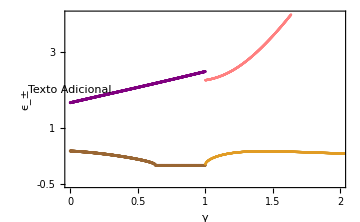

```mathematica
Clear[ηx,ηy,ηz,ξ]
ηx=0;
ηy=0.9;
ηz=0;
ξ=0;
xc[ηx,ηy,ηz,ξ]
yc[ηx,ηy,ηz,ξ]
lim[ηx,ηy,ηz,ξ]
texto=Graphics[{Text["Punto de interés",{0,2}]},PlotRange->All];
Show[p[ηx,ηy,ηz,ξ,cT,cB,0,0,0,0,0,0,0,0],Epilog->{Text["Texto Adicional",{0,2}]}]
```

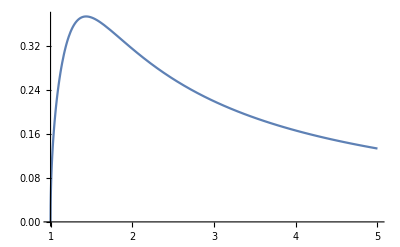

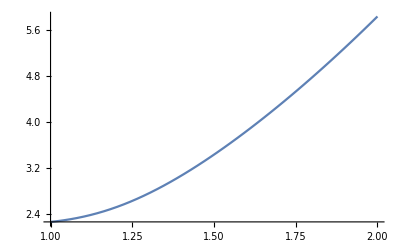

{0.373654,{γ→1.43516}}

```mathematica
Plot[Re[(ϵ1ms[ηz,ηx,γ,ξ]*ϵ2ms[ηz,ηx,ηy,γ,ξ])],{γ,xc[ηx,ηy,ηz,ξ],5}]
Plot[Re[(ϵ1ps[ηz,ηx,γ,ξ]*ϵ2ps[ηz,ηx,ηy,γ,ξ])],{γ,xc[ηx,ηy,ηz,ξ],2}]
Maximize[{Re[(ϵ1ms[ηz,ηx,γ,ξ]*ϵ2ms[ηz,ηx,ηy,γ,ξ])],xc[ηx,ηy,ηz,ξ]<=γ<=2},γ]
```

```mathematica
Sqrt[ω*ωo]/(1+ξ)*Sqrt[1-(ηz-ηx)/ωo]
```

0.474342